## Brian — PS 4 — 2025-01-29 — Solution

## EIWL3 Second Half of Section 11, and Sections 12 and 13

## Exercises 11.16 to 11.31 from EIWL3 Section 11

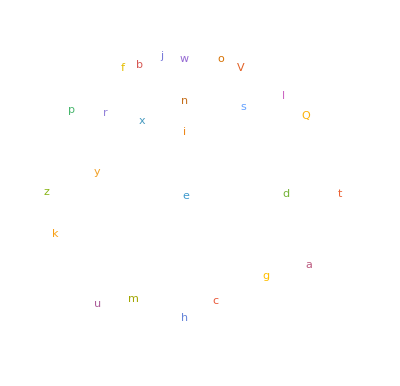

```mathematica
(* 11.16 *) WordCloud[StringTake[StringReverse[WordList[]],1]]
```

```mathematica
(* 11.17 *) RomanNumeral[1959]
```

MCMLIX

```mathematica
(* 11.18 *) Max[StringLength[RomanNumeral[Range[2020]]]]
```

13

```mathematica
(* 11.19 *) WordCloud[StringTake[RomanNumeral[Range[2020]],1]]
```

-Graphics-

```mathematica
(* 11.20 *) Length[Alphabet["Russian"]]
```

33

```mathematica
(* 11.21 *) ToUpperCase[Alphabet["Greek"]]
```

{Α,Β,Γ,Δ,Ε,Ζ,Η,Θ,Ι,Κ,Λ,Μ,Ν,Ξ,Ο,Π,Ρ,Σ,Τ,Υ,Φ,Χ,Ψ,Ω}

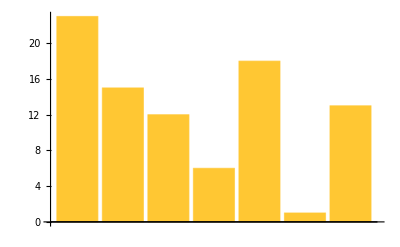

```mathematica
(* 11.22 *) BarChart[LetterNumber[Characters["wolfram"]]]
```

```mathematica
(* 11.23 *) StringJoin[FromLetterNumber[RandomInteger[25,1000]+1]]
```

ubiirjnmgvbynfonmrwmglctmqxiegjtjwolvzelbjbfwbfklklfrmwcxsqpjnjxxcpmdyrumsigtizqxtubmocgnlfeitlteugsoftervlyxsfbdtlrmhmfmzcidjsdgumsvarytcnsoocuruulrsylopyucdwjdvdfvtntruylalqobkorydgvvwkpobszsnsltdlwjbvsjsuhanlivzgthjvfpejytmnupaogqxqtniblykilvvegcddxvgemsoggflgfchtigytrjhshvwenokgpddhahzgiizctbsumoowelspopfrsnmtdksmjtpadchxivylyreevqaltzxbpulsvvyrungxlibhifzvkmujhnfcscbigvdkmavirhkbjweyoepvrrrorxoiapzqepqfforcyktvaeucqimczoysgyqlizzneoxkhnjkmoafzjrowzekfshsrurpafksiellxfxqtmmtugtsiprstjaeegdpmsyjcouccudeafuvjnbheraeljhxtpblufuehrdjrnbnrnmhsxkvmpmeoppjzknijpnvwyzcgccgfdnhomchkzucmwmcrlfjmhqnnkgtygcrzbrvbjqawinqjidvukendwujcuqjwwdvvsvduvfoouvtkbjqxhkzvmejunopgzsskzymlymmxnkeecripammpcxxzauwcxowduwpdpcdobebfylsgokfutdaufbafyyhngkkwrabiqnmntnkpazncyjcniqzjtuerwwnihzewhixvissusbvbfkgykdbchvyxqrhiwcxvwbualadssurdplnqgfirlpmmebpifjmoawfrxhnyquduqwjnoniplbawlcxtsudmbxurmahopdpnxqtkkoivoaemnzhmlzgxvjfqxwnteclgyhuvnafuelqtgjdetychfenfxxgzrwbytepilyvuupgxahsdlcruazcoroougiqmfkvcpfszpegbjctuylpa

```mathematica
(* 11.24 *) Table[StringJoin[FromLetterNumber[RandomInteger[25,5]+1]],100]
```

{eblfg,anhaw,lsiad,lmpvk,xalsb,rwovk,talrp,iaqgd,zewzf,achyo,fvlkk,sjnwp,nolya,hxoxu,xqeem,jbdoo,gwbdp,mjwae,cdzef,zwdnr,quqqj,gusig,kixdf,bouxc,uecyp,kuxxy,eisvn,sdawz,jskdx,zjerh,umqxm,yinhk,uplxh,garhg,tvaou,jlppz,rwvag,cbrcx,gftxa,ahupx,ezmfj,vuxtz,lvyrh,klgup,chcnc,uculz,gmrwm,qqvhw,ktnqs,ynpxu,cqctt,afkff,tbqbb,tcotq,suius,tnqhx,szkov,tlems,jypuk,qyepq,sibpr,ntjse,cjxdu,fyyfb,oioyd,tgrgi,finhv,gzvpj,ctqdf,jbgme,sdpak,vqpwu,apqjl,xcezb,pyzsa,bavju,czjda,bwfij,ioffz,nortx,gztou,pbvul,tplfw,qtkpg,xuyjg,sumnq,zygxu,nfjvs,pwgar,csdye,wnjfz,gwswb,zjqyg,tjarn,oiwun,ntajt,pkxrs,zkyoe,izvzb,azllp}

```mathematica
(* 11.25 *) Transliterate["wolfram", "Greek"]
```

βολφραμ

```mathematica
(* 11.26 *)StringJoin[Table[{ Entity["TaxonomicSpecies","CanisLupus::7z843"][EntityProperty["TaxonomicSpecies","Emoji"]],Entity["TaxonomicSpecies","OvisAries::4t8r2"][EntityProperty["TaxonomicSpecies","Emoji"]][[2]]},10]]
```

🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏

```mathematica
(* 11.27*) Transliterate[Alphabet["Arabic"]]
```

{a,b,t,th,j,h,kh,d,dh,r,z,s,sh,s,d,t,z,ʿ,gh,f,q,k,l,m,n,h,w,y}

```mathematica
(* 11.28 *) ColorNegate[Rasterize[Style["A",200]]]
```

-Graphics-

```mathematica
(* 11.29 *) Manipulate[Style[FromLetterNumber[letterNumber],100], {letterNumber,1,26,1}]
```

```mathematica
(* 11.30 *) Manipulate[ColorNegate[EdgeDetect[Rasterize[Style[FromLetterNumber[letterNumber],100]]]], {letterNumber,1,26,1}]
```

```mathematica
Blur[Rasterize[Style["A",100]],50]
```

-Graphics-

```mathematica
(* 11.31 *) Manipulate[Blur[Rasterize[Style["A",100]],blur], {blur,0,50}]
```

## Exercises from EIWL3 Section 12

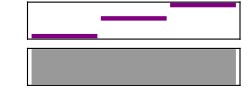

```mathematica
(* 12.1 *)Sound[ Table[SoundNote[n],{n,{0,4,7}}]]
```

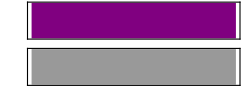

```mathematica
(* 12.2 *)Sound[SoundNote["A",2]]
```

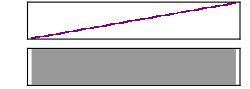

```mathematica
(* 12.3 *)Sound[Table[SoundNote[pitch,0.05],{pitch,0,48}]]
```

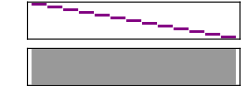

```mathematica
(* 12.4 *)Sound[Table[SoundNote[pitch,0.5],{pitch,12,0,-1}]]
```

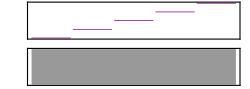

```mathematica
(* 12.5 *)Sound[Table[SoundNote[12pitch,0.5],{pitch,0,4}]]
```

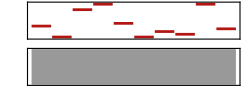

```mathematica
(* 12.6 *)Sound[Table[SoundNote[RandomInteger[12],0.2,"Trumpet"],10]]
```

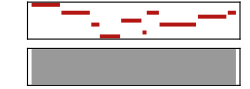

```mathematica
(* 12.7 *)Sound[Table[SoundNote[RandomInteger[12],(RandomInteger[9]+1)/10,"Trumpet"],10]]
```

```mathematica
IntegerDigits[2^31]
```

{2,1,4,7,4,8,3,6,4,8}

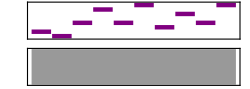

```mathematica
(* 12.8 *)Sound[Table[SoundNote[pitch,0.1],{pitch,IntegerDigits[2^31]}]]
```

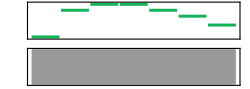

```mathematica
(* 12.9 *)Sound[Table[SoundNote[pitch,0.1, "Guitar"],{pitch,Characters["CABBAGE"]}]]
```

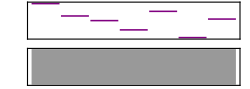

```mathematica
(* 12.10 *)Sound[Table[SoundNote[n,0.1],{n,LetterNumber[Characters["wolfram"]]}]]
```

## Exercises from EIWL3 Section 13

```mathematica
(* 13.1 *) Grid[Table[x y,{x,1,12},{y,1,12}]]
(* It is worth noting (even though this table is symmetrical), that x is on the vertical axis. *)
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144

```mathematica
(* 13.2 *) Grid[Table[RomanNumeral[x y],{x,1,5},{y,1,5}]]
(* Same note as above. *)
```

I | II | III | IV | V
II | IV | VI | VIII | X
III | VI | IX | XII | XV
IV | VIII | XII | XVI | XX
V | X | XV | XX | XXV

```mathematica
(* 13.3 *) Grid[Table[RandomColor[],10,10]]
(* Same note as above. *)
```

RGBColor[0.8285707203223471, 0.28503092881479386, 0.5935792727674936] | RGBColor[0.9642170436455788, 0.2593519241760178, 0.797614715072468] | RGBColor[0.05828606771853262, 0.4604077440950909, 0.04908725004742154] | RGBColor[0.9815681898874533, 0.5946617718769309, 0.5633539308027744] | RGBColor[0.28637655995768396, 0.8558337018221482, 0.7384697567625615] | RGBColor[0.3063405016582681, 0.14040372276834168, 0.8687671543689617] | RGBColor[0.1543820367179034, 0.808186878782424, 0.7865692977040719] | RGBColor[0.1691172383569195, 0.3774474914474357, 0.6616804627007788] | RGBColor[0.33919461072249213, 0.2156756398925852, 0.010591300350686561] | RGBColor[0.7813140301301384, 0.4897739140898203, 0.5317473469309022]
RGBColor[0.33393766180100326, 0.3725687294850286, 0.5684390783911921] | RGBColor[0.30352678460427507, 0.8223100534455194, 0.8459847509364917] | RGBColor[0.6538394073763445, 0.016461781654548036, 0.21244556268081016] | RGBColor[0.49208795022206453, 0.4478513067047518, 0.9709117469189941] | RGBColor[0.4420953412451507, 0.2029118114493711, 0.18067722192043822] | RGBColor[0.6016649078551191, 0.33507916968916507, 0.11269849023062384] | RGBColor[0.13757048901184787, 0.22397362443650315, 0.6996524606364367] | RGBColor[0.9498230788791076, 0.27790483504885666, 0.6525407759703454] | RGBColor[0.04770633413239356, 0.039382558298441284, 0.36533885156781665] | RGBColor[0.7866843829414878, 0.26137651732865486, 0.6555745751731441]
RGBColor[0.8313242823281317, 0.2981864532370573, 0.8714606700360066] | RGBColor[0.9087772332395947, 0.5929591095935918, 0.13495072667353525] | RGBColor[0.06745966092472266, 0.21950415294987846, 0.7292650572691666] | RGBColor[0.7907916554279426, 0.9688532606502172, 0.07807313778878022] | RGBColor[0.6191736193189883, 0.02298217514996459, 0.9115228982802477] | RGBColor[0.4986811951594585, 0.857485793378844, 0.7467693690585029] | RGBColor[0.394922134286416, 0.22018067274690778, 0.852064858474948] | RGBColor[0.7892864441429941, 0.8874372494493425, 0.4985925706023653] | RGBColor[0.4447548005429707, 0.8523212667354638, 0.6747022207056068] | RGBColor[0.3897985432854789, 0.7334323520870072, 0.37238884975915365]
RGBColor[0.8344540304735792, 0.7719371110272173, 0.08053222341553279] | RGBColor[0.7473094081158376, 0.3341090821935784, 0.7380032475667473] | RGBColor[0.2883661917801885, 0.14055948099990312, 0.08844250894704087] | RGBColor[0.23382794766303783, 0.328491657601913, 0.7245799832858593] | RGBColor[0.018958549781403766, 0.09047037261223356, 0.6799573571520308] | RGBColor[0.25970684257661514, 0.8602389580471959, 0.41423905896203483] | RGBColor[0.42010133733766875, 0.5275511255286249, 0.7191792401700472] | RGBColor[0.014780389929187843, 0.8782153934380914, 0.21698952632077706] | RGBColor[0.6224503569363762, 0.456807392738265, 0.10659124741491022] | RGBColor[0.6029474951288765, 0.5389294082101193, 0.43064412352746184]
RGBColor[0.27698467816922734, 0.7938733214843792, 0.28609402251136395] | RGBColor[0.40146048895012987, 0.8536346624042361, 0.6032000176727315] | RGBColor[0.7660441223825936, 0.4109699202274566, 0.43675685775444584] | RGBColor[0.5193697549924872, 0.47228159038203343, 0.9240802372542127] | RGBColor[0.8068725163820878, 0.802458075305533, 0.7777296045676139] | RGBColor[0.5805895406136701, 0.9279718261888934, 0.15246589539258948] | RGBColor[0.4546023876250873, 0.0180884736443101, 0.5812673924428549] | RGBColor[0.4901964833664483, 0.301137055236949, 0.690885547275907] | RGBColor[0.08731677390518122, 0.8946310730208455, 0.9095216942811941] | RGBColor[0.2916519860650313, 0.6496039262896867, 0.9913992433295384]
RGBColor[0.002365578016354508, 0.7563191488714942, 0.6400320339657226] | RGBColor[0.6646453126033185, 0.08176412213081985, 0.43441994207790247] | RGBColor[0.4749011415298774, 0.389867095180207, 0.0021039557906916695] | RGBColor[0.5493491829195931, 0.19235752620328128, 0.9901174193232538] | RGBColor[0.09961378081379535, 0.6180843515538712, 0.8400075893507313] | RGBColor[0.07336621589099956, 0.8955462500861819, 0.4444669072386831] | RGBColor[0.6041286697418082, 0.28304660870428955, 0.5288729103880814] | RGBColor[0.9701200009177775, 0.2946018847570411, 0.9635895094161873] | RGBColor[0.8334681409345988, 0.7732053757991924, 0.46683936111266155] | RGBColor[0.8246880107132908, 0.6978436773004197, 0.7083119848022363]
RGBColor[0.11886921165834963, 0.27166451224046595, 0.24070996956915525] | RGBColor[0.6084358128213665, 0.47196367332280187, 0.1760352567600576] | RGBColor[0.5115205072637647, 0.7298259535897866, 0.6781731516558811] | RGBColor[0.5664805445186121, 0.13255183216144295, 0.053912164123103956] | RGBColor[0.39791931512164513, 0.29448179913680494, 0.6801086411290376] | RGBColor[0.04231479987156472, 0.12688886698172164, 0.7282265251191335] | RGBColor[0.010635873696414722, 0.17214692497016681, 0.1858739359510999] | RGBColor[0.9388527537129263, 0.7401981763729706, 0.9113949939781227] | RGBColor[0.18918708306776177, 0.49091023155209657, 0.37326460530021155] | RGBColor[0.9840059492357833, 0.03546514781829968, 0.8727916892661272]
RGBColor[0.3243045654547645, 0.23214603837035552, 0.7746993168398715] | RGBColor[0.6845412180049397, 0.2075631881024671, 0.5281468592508514] | RGBColor[0.21282824371603004, 0.24565512045413151, 0.9048317649920796] | RGBColor[0.21117373685656426, 0.5429119016999484, 0.18202522841901603] | RGBColor[0.9498897045971681, 0.20937775427563454, 0.1311622115113753] | RGBColor[0.4178951465496783, 0.7606776757215883, 0.3167128913950874] | RGBColor[0.6029912374610262, 0.2961145961970255, 0.9590368971344718] | RGBColor[0.9392270452241294, 0.8212448213040131, 0.5218510791490527] | RGBColor[0.3452334896147946, 0.4183560007401588, 0.10533217460581756] | RGBColor[0.30518627551558675, 0.5671068868312545, 0.8023508035062938]
RGBColor[0.7607479392914058, 0.7874238149374124, 0.48908137243345284] | RGBColor[0.9785557216312801, 0.20036486942632692, 0.7590789380209118] | RGBColor[0.22205764228613312, 0.3596437686985652, 0.5261665743399193] | RGBColor[0.29240346693849695, 0.21308454217951533, 0.44469675116719465] | RGBColor[0.12607878893149427, 0.16674961201996963, 0.9315530915361279] | RGBColor[0.8994002109322392, 0.6340254597134067, 0.5766070295495009] | RGBColor[0.9517401918041093, 0.6295019601148275, 0.31967132104098384] | RGBColor[0.8344206768842517, 0.1229803021204412, 0.8837463990582242] | RGBColor[0.30253959277989484, 0.3736639675489153, 0.04137196602022497] | RGBColor[0.8133448949692099, 0.00601274570343624, 0.5383080328884118]
RGBColor[0.05783280994932949, 0.46378206616075013, 0.08016890953465516] | RGBColor[0.48724980254131567, 0.19292546917258635, 0.644364219254816] | RGBColor[0.23969843818584669, 0.8091945009924499, 0.49328907541619715] | RGBColor[0.8923226579534613, 0.5844695082297442, 0.9749460894548219] | RGBColor[0.8339995715821722, 0.014065693099950316, 0.5399649615600677] | RGBColor[0.4526760334481976, 0.1237958878095411, 0.10138748028499278] | RGBColor[0.360113452643968, 0.5769064372222112, 0.7670253047194946] | RGBColor[0.005547680897061147, 0.2053508868904903, 0.18256725577795296] | RGBColor[0.2005020223267746, 0.9149423326512858, 0.4756048511005657] | RGBColor[0.7511924524911369, 0.19720527100084762, 0.6865979235528628]

```mathematica
(* 13.4 *) Grid[Table[Style[RandomInteger[10],RandomColor[]],10,10]]
(* Same note as above. *)
```

9 | 8 | 2 | 8 | 9 | 9 | 1 | 3 | 2 | 10
0 | 10 | 4 | 3 | 8 | 9 | 3 | 0 | 6 | 10
6 | 9 | 6 | 7 | 0 | 10 | 9 | 8 | 8 | 2
8 | 8 | 10 | 4 | 1 | 8 | 7 | 5 | 4 | 1
9 | 9 | 1 | 6 | 5 | 4 | 4 | 9 | 10 | 7
9 | 10 | 8 | 10 | 4 | 7 | 3 | 0 | 10 | 6
10 | 10 | 7 | 10 | 1 | 5 | 2 | 6 | 5 | 5
8 | 8 | 6 | 3 | 0 | 7 | 3 | 3 | 6 | 5
4 | 9 | 0 | 9 | 7 | 10 | 10 | 5 | 3 | 1
6 | 9 | 9 | 5 | 10 | 10 | 9 | 5 | 2 | 0

```mathematica
(* 13.5 *) Grid[Table[StringJoin[{a1,a2}],{a1,Alphabet[]},{a2,Alphabet[]}]]
```

aa | ab | ac | ad | ae | af | ag | ah | ai | aj | ak | al | am | an | ao | ap | aq | ar | as | at | au | av | aw | ax | ay | az
ba | bb | bc | bd | be | bf | bg | bh | bi | bj | bk | bl | bm | bn | bo | bp | bq | br | bs | bt | bu | bv | bw | bx | by | bz
ca | cb | cc | cd | ce | cf | cg | ch | ci | cj | ck | cl | cm | cn | co | cp | cq | cr | cs | ct | cu | cv | cw | cx | cy | cz
da | db | dc | dd | de | df | dg | dh | di | dj | dk | dl | dm | dn | do | dp | dq | dr | ds | dt | du | dv | dw | dx | dy | dz
ea | eb | ec | ed | ee | ef | eg | eh | ei | ej | ek | el | em | en | eo | ep | eq | er | es | et | eu | ev | ew | ex | ey | ez
fa | fb | fc | fd | fe | ff | fg | fh | fi | fj | fk | fl | fm | fn | fo | fp | fq | fr | fs | ft | fu | fv | fw | fx | fy | fz
ga | gb | gc | gd | ge | gf | gg | gh | gi | gj | gk | gl | gm | gn | go | gp | gq | gr | gs | gt | gu | gv | gw | gx | gy | gz
ha | hb | hc | hd | he | hf | hg | hh | hi | hj | hk | hl | hm | hn | ho | hp | hq | hr | hs | ht | hu | hv | hw | hx | hy | hz
ia | ib | ic | id | ie | if | ig | ih | ii | ij | ik | il | im | in | io | ip | iq | ir | is | it | iu | iv | iw | ix | iy | iz
ja | jb | jc | jd | je | jf | jg | jh | ji | jj | jk | jl | jm | jn | jo | jp | jq | jr | js | jt | ju | jv | jw | jx | jy | jz
ka | kb | kc | kd | ke | kf | kg | kh | ki | kj | kk | kl | km | kn | ko | kp | kq | kr | ks | kt | ku | kv | kw | kx | ky | kz
la | lb | lc | ld | le | lf | lg | lh | li | lj | lk | ll | lm | ln | lo | lp | lq | lr | ls | lt | lu | lv | lw | lx | ly | lz
ma | mb | mc | md | me | mf | mg | mh | mi | mj | mk | ml | mm | mn | mo | mp | mq | mr | ms | mt | mu | mv | mw | mx | my | mz
na | nb | nc | nd | ne | nf | ng | nh | ni | nj | nk | nl | nm | nn | no | np | nq | nr | ns | nt | nu | nv | nw | nx | ny | nz
oa | ob | oc | od | oe | of | og | oh | oi | oj | ok | ol | om | on | oo | op | oq | or | os | ot | ou | ov | ow | ox | oy | oz
pa | pb | pc | pd | pe | pf | pg | ph | pi | pj | pk | pl | pm | pn | po | pp | pq | pr | ps | pt | pu | pv | pw | px | py | pz
qa | qb | qc | qd | qe | qf | qg | qh | qi | qj | qk | ql | qm | qn | qo | qp | qq | qr | qs | qt | qu | qv | qw | qx | qy | qz
ra | rb | rc | rd | re | rf | rg | rh | ri | rj | rk | rl | rm | rn | ro | rp | rq | rr | rs | rt | ru | rv | rw | rx | ry | rz
sa | sb | sc | sd | se | sf | sg | sh | si | sj | sk | sl | sm | sn | so | sp | sq | sr | ss | st | su | sv | sw | sx | sy | sz
ta | tb | tc | td | te | tf | tg | th | ti | tj | tk | tl | tm | tn | to | tp | tq | tr | ts | tt | tu | tv | tw | tx | ty | tz
ua | ub | uc | ud | ue | uf | ug | uh | ui | uj | uk | ul | um | un | uo | up | uq | ur | us | ut | uu | uv | uw | ux | uy | uz
va | vb | vc | vd | ve | vf | vg | vh | vi | vj | vk | vl | vm | vn | vo | vp | vq | vr | vs | vt | vu | vv | vw | vx | vy | vz
wa | wb | wc | wd | we | wf | wg | wh | wi | wj | wk | wl | wm | wn | wo | wp | wq | wr | ws | wt | wu | wv | ww | wx | wy | wz
xa | xb | xc | xd | xe | xf | xg | xh | xi | xj | xk | xl | xm | xn | xo | xp | xq | xr | xs | xt | xu | xv | xw | xx | xy | xz
ya | yb | yc | yd | ye | yf | yg | yh | yi | yj | yk | yl | ym | yn | yo | yp | yq | yr | ys | yt | yu | yv | yw | yx | yy | yz
za | zb | zc | zd | ze | zf | zg | zh | zi | zj | zk | zl | zm | zn | zo | zp | zq | zr | zs | zt | zu | zv | zw | zx | zy | zz

```mathematica
(* 13.6 *)
toVisualize={1,4,3,5,2};
Grid[{
{PieChart[toVisualize],NumberLinePlot[toVisualize]},
{ListLinePlot[toVisualize],BarChart[toVisualize]}
}]
```

-Graphics-

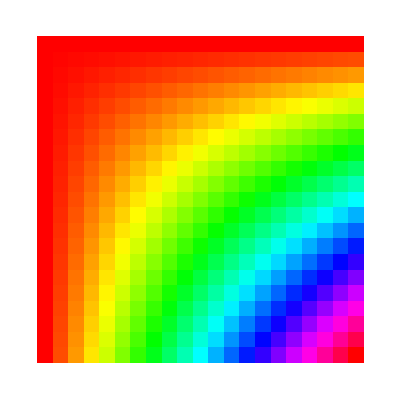

```mathematica
(* 13.7 *)ArrayPlot[
Table[Hue[i j],{i,Range[0,1,0.05]}, {j,Range[0,1,0.05]}]
]
```

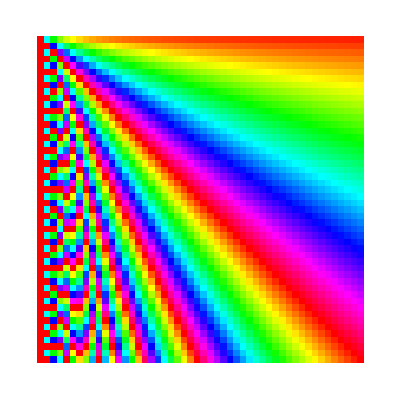

```mathematica
(* 13.8 *) ArrayPlot[
Table[Hue[i /j],{i,Range[50]}, {j,Range[50]}]
]
```

```mathematica
(* 13.9 *) ArrayPlot[
Table[StringLength[RomanNumeral[i j]],{i,Range[100]}, {j,Range[100]}]
]
```

-Graphics-